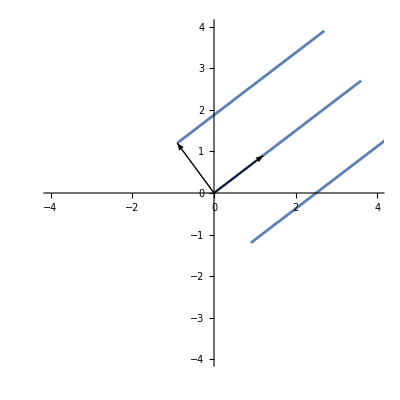

```mathematica
p1=ParametricPlot[{x,2.7/3.6 x},{x,0,3.6}];
p2=ParametricPlot[{x,2.7/3.6 x+1.2+0.9 2.7/3.6},{x,-0.9,-0.9+3.6}];
p3=ParametricPlot[{x,2.7/3.6 x-1.2-0.9 2.7/3.6},{x,0.9,0.9+3.6}];
v1={3.6,2.7};
a1=Arrow[{{0,0},v1/3}];
v2={-2.7,3.6};
a2=Arrow[{{0,0},v2/3}];
Show[{p1,p2,p3},Graphics[{a1,a2}],AspectRatio->1,PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
1.2+0.9 2.7/3.6
```

1.875

```mathematica
-1.2-0.9 2.7/3.6
```

-1.875

```mathematica
Solve[0==2.7/3.6 x-1.2-0.9 2.7/3.6]
```

{{x→2.5}}

```mathematica
2.7/3.6 x-1.2-0.9 2.7/3.6/.x->1.8
```

-0.525

```mathematica
2.7/3.6 x/.x->4.4
```

3.3

```mathematica
v2/Norm[v2]
```

{-0.6,0.8}